```mathematica
SetDirectory["/Users/sejin/cursor/kias/holography/3D/onnx"];

Do[
net[i]=Import["model_"<>ToString[i]<>".onnx","NetExternalObject"]
,{i,1,101}]
```

```mathematica
predict[lzt_]:=Module[{result,tgt},

tgt=ArrayReshape[Table[1,{i,Dimensions[lzt][[1]]}],{Dimensions[lzt][[1]],1,1}]//N;
out=tgt;
Do[
result=net[i][<|"src"->lzt,"tgt"->tgt|>];
tgt=MapThread[Append,{tgt,result[[All,-1]]}]//N;
out=tgt;
,{i,1,100}];
tgt
]
findlzt[pp_]:=Module[{lzt},lzt =Table[Table[l/.FindRoot[D[S[l],l]==1/(2 zt)/.zh-> 1+10^-5/.p->pp[[i]],{l,10^-5}],{zt,0+10^-7,1+10^-7,0.01}],{i,Length[pp]}];
lzt=ArrayReshape[N[lzt],{Length[pp],101,1}];
lzt]
plotf[data_]:= ListPlot[Evaluate[Table[Transpose[{Table[i,{i,0,1,0.01}][[;;Length[data[[j]]]]],data[[j,All,1]]}],{j,Length[data]}]][[All,;;;;2]](*,Joined->True*),AxesLabel->{z,f[z]}(*,PlotLegends->plist*),PlotStyle->Directive[PointSize[0.013]],PlotRange->All]
```

#### BTZ

S[l]=L/(2 G_3)Log[(2zh)/ϵ_UV Sinh[l/(2zh)]]

```mathematica
S[l_]:=If[p==1,Log[l]](*Log[(2zh)/Subscript[ϵ, UV] Sinh[l/(2zh)]];*)
plist={_};
```

```mathematica
Dynamic[plotf[out]]
```

```mathematica
lzt=findlzt[{1}];
out = predict[lzt];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.998711}. NIntegrate obtained 7.14337-3.18219 ⅈ and 0.0664485 for the integral and error estimates.

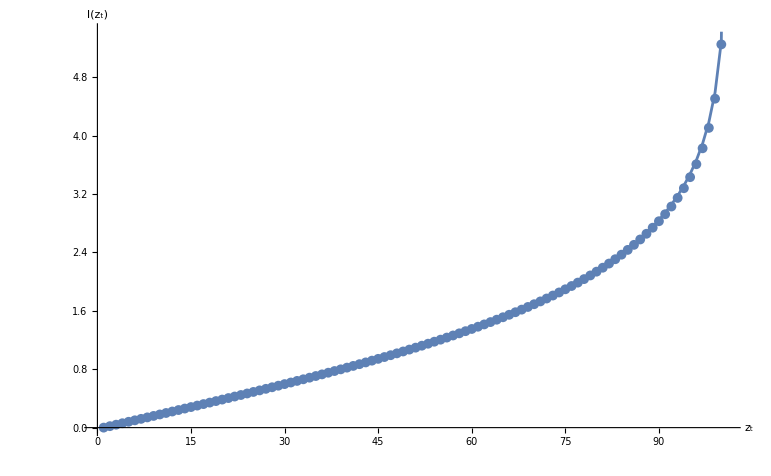

```mathematica
Table[NIntegrate[(2 z)/(√(-z^2 +z0^2))1/(√f[z])/.f->Function[{z1},Interpolation[Transpose[{Table[i,{i,0,1,0.01}][[;;Length[out[[j]]]]],out[[j,All,1]]}]][z1]],{z,0,z0}],{j,Length[out]},{z0,0,1,0.01}];
Show[{ListPlot[lzt[[All,All,1]],AxesLabel->{Subscript[z, t],l[Subscript[z, t]]},Joined->True],ListPlot[%,AxesLabel->{Subscript[z, t],l[Subscript[z, t]]}]}]
```

#### Tanh[l/(2zh)p]ⅇ^(l/(2zh))

S[l]=L/(2 G_3)Log[(2zh)/(ϵ_UV p) Tanh[l/(2zh)p]ⅇ^(l/(2zh))]

```mathematica
S[l_]:=Log[(2zh)/(Subscript[ϵ, UV] p) Tanh[l/(2zh)p] ⅇ^(l/(2zh))];
(*plist=Table[0.1i+0.5,{i,0,25}];*)
plist=Table[0.5i+0.5,{i,0,5}];
(*plist=Table[0.1i+0.1,{i,0,5}];*)
```

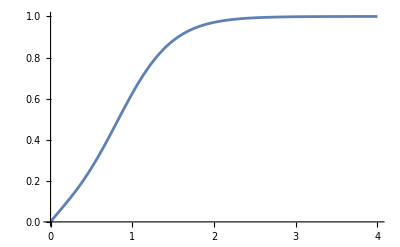

```mathematica
Plot[1/(2S'[l])/.zh->1 /.p-> 3//Simplify,{l,0,4}]
```

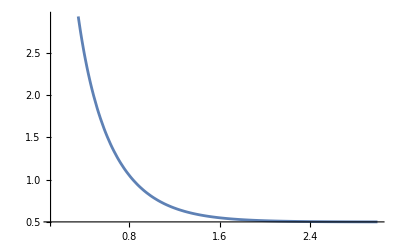

```mathematica
Plot[Evaluate[S'[l]/.zh-> 1/.p->3],{l,0.1,3}]
```

```mathematica
Dynamic[Show[plotf[out](*,Plot[1-z,{z,0,1},PlotStyle-> Gray]*)]]
```

```mathematica
lzt=findlzt[plist]; 
out = predict[lzt];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.919043}. NIntegrate obtained 8.74849-2.2946 ⅈ and 0.05814 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.92914}. NIntegrate obtained 8.2726-2.74907 ⅈ and 0.156018 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.92914}. NIntegrate obtained 7.33747-1.41208 ⅈ and 0.0527063 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

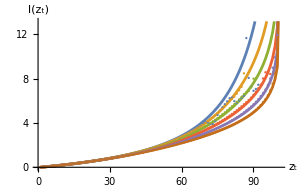

```mathematica
rlzt=Table[NIntegrate[(2 z)/(√(-z^2 +z0^2))1/(√f[z])/.f->Function[{z1},Interpolation[Transpose[{Table[i,{i,0,1,0.01}][[;;Length[out[[j]]]]],out[[j,All,1]]}]][z1]],{z,0,z0}],{j,Length[out]},{z0,0,1,0.01}];
Show[{ListPlot[lzt[[All,All,1]],AxesLabel->{Subscript[z, t],l[Subscript[z, t]]},Joined->True],ListPlot[rlzt,AxesLabel->{Subscript[z, t],l[Subscript[z, t]]}]}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

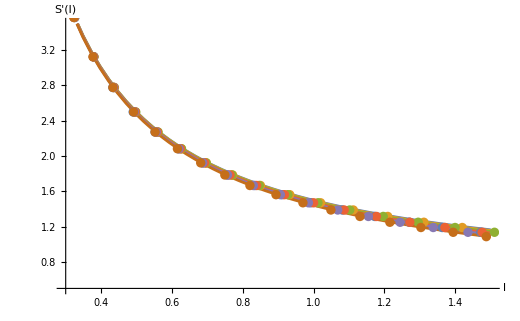

```mathematica
Show[Plot[S'[l]/. p->plist/.zh-> 1//Evaluate,{l,0.3,1.5},AxesLabel->{l,"S"'[l]},PlotRange->{0.5,3.5}],ListPlot[Table[Transpose[{rlzt[[i]],1/(2Table[z0,{z0,0,1,0.01}])}][[;;;;2]],{i,Length[rlzt]}],PlotTheme->"Detailed",PlotStyle->Directive[PointSize[0.013]]]]
```

```mathematica
zpf=Table[{Table[0.01 j ,{j,0,100}][[j]],plist[[i]],out[[i,j,1]]},{i,Length[plist]},{j,100}];
zpf=Flatten[zpf,1];
```

```mathematica
model=GeneralizedLinearModelFit[zpf,{x(*,y*),x^2,x y(*,y^2*),x^3(*,y^3*),x^2 y,x y^2,x^4,(*y^4,*)(*x y^3,*)y x^3,x^2 y^2,x^5(*,y^5*),x^4 y(*,y^4 x*)(*,x^3 y^2*),x^2 y^3,x^6(*,y^6*),x^5 y(*, y^5 x*),x^4 y^2(*,y^4 x^2*),x^3 y^3},{x,y}];
fittedFunction=model["Function"][z,p];
(#[[3]]-fittedFunction/.Thread[{z,p}-> #[[{1,2}]]])^2/Length[zpf]&/@zpf//Total
Collect[fittedFunction//FullSimplify,z]
```

6.77564×10^-6

1.00002+(-1.96978-0.740627 p+0.202323 p^2) z+(-4.67945+8.05155 p+0.332988 p^2-0.0885572 p^3) z^2+(20.9891-20.3303 p+0.0985536 p^3) z^3+(-29.1723+20.6611 p-0.569248 p^2) z^4+(17.3229-7.60371 p) z^5-3.49971 z^6

```mathematica
Show[{ListPlot3D[zpf,PlotStyle->Gray],Plot3D[{fittedFunction},{z,0,1},{p,0.5,3},PlotPoints->30]}]
```

-Graphics3D-

```mathematica
out={{{1.},{0.9760064482688904},{0.9511681795120239},{0.9272245764732361},{0.9038649797439575},{0.8804214596748352},{0.8579581379890442},{0.8354482054710388},{0.8135961890220642},{0.79218989610672},{0.7708328366279602},{0.7500002980232239},{0.7296332716941833},{0.7098161578178406},{0.6908139586448669},{0.6725647449493408},{0.654305100440979},{0.6360307931900024},{0.6184264421463013},{0.6011252999305725},{0.5844545960426331},{0.5686514973640442},{0.5533654093742371},{0.5379318594932556},{0.5222464799880981},{0.5073151588439941},{0.4928022027015686},{0.4788767099380493},{0.4654184877872467},{0.4519118368625641},{0.43844395875930786},{0.4257441759109497},{0.41385775804519653},{0.4021960496902466},{0.390830934047699},{0.3794143795967102},{0.36786478757858276},{0.35673242807388306},{0.34662115573883057},{0.3372640609741211},{0.32776838541030884},{0.3180904686450958},{0.3086240291595459},{0.2990064024925232},{0.2900696098804474},{0.2820686101913452},{0.2748931348323822},{0.26748350262641907},{0.25919362902641296},{0.25081101059913635},{0.24261106550693512},{0.23526546359062195},{0.22881753742694855},{0.22272749245166779},{0.21626916527748108},{0.2093230038881302},{0.2026100903749466},{0.19679565727710724},{0.1910565048456192},{0.1857433319091797},{0.18011926114559174},{0.17424367368221283},{0.16828419268131256},{0.16294562816619873},{0.15784798562526703},{0.1527768224477768},{0.1475968211889267},{0.14232860505580902},{0.13688071072101593},{0.13178396224975586},{0.12698416411876678},{0.1219705268740654},{0.11772005259990692},{0.11335960030555725},{0.10870373994112015},{0.10400377959012985},{0.09931345283985138},{0.09500773996114731},{0.0908241868019104},{0.08670677989721298},{0.08272227644920349},{0.07839535921812057},{0.07416512817144394},{0.06983672082424164},{0.06536975502967834},{0.06176149845123291},{0.05817139893770218},{0.05423358827829361},{0.05050642788410187},{0.046406589448451996},{0.042355697602033615},{0.03805988281965256},{0.03378982096910477},{0.030880039557814598},{0.027623267844319344},{0.021562818437814713},{0.015444792807102203},{0.008704965934157372},{0.0077855996787548065},{0.002500191330909729},{-0.0021323207765817642}},{{1.},{0.9760839939117432},{0.9506118893623352},{0.9271158576011658},{0.9039011597633362},{0.8805521130561829},{0.8583657145500183},{0.8362764716148376},{0.8148506283760071},{0.7939026951789856},{0.7729660868644714},{0.752602756023407},{0.7326889038085938},{0.7132964730262756},{0.6949352622032166},{0.6770848631858826},{0.6594408750534058},{0.6416694521903992},{0.6248113512992859},{0.608276903629303},{0.5924550294876099},{0.5773438811302185},{0.5626996159553528},{0.5477834939956665},{0.5329756736755371},{0.5188155770301819},{0.5054064989089966},{0.49229422211647034},{0.4796104431152344},{0.4670572280883789},{0.45431360602378845},{0.44229650497436523},{0.4311444163322449},{0.4204252362251282},{0.4098377227783203},{0.39935946464538574},{0.3887431025505066},{0.3784862458705902},{0.3689752221107483},{0.36015576124191284},{0.3514614701271057},{0.34264594316482544},{0.33374881744384766},{0.32491523027420044},{0.3166314959526062},{0.30929887294769287},{0.30270153284072876},{0.2956658601760864},{0.287792444229126},{0.28013166785240173},{0.27260759472846985},{0.26573801040649414},{0.2595027685165405},{0.2539002597332001},{0.2476591020822525},{0.2409820705652237},{0.23457427322864532},{0.22917692363262177},{0.22410909831523895},{0.21928925812244415},{0.21425466239452362},{0.20865334570407867},{0.20311298966407776},{0.1978306919336319},{0.19294875860214233},{0.1880810558795929},{0.18314231932163239},{0.17776525020599365},{0.17215904593467712},{0.16652236878871918},{0.16144751012325287},{0.15661205351352692},{0.15168465673923492},{0.1466568410396576},{0.14165787398815155},{0.1364368498325348},{0.13105040788650513},{0.12573480606079102},{0.12058478593826294},{0.1154223158955574},{0.11036261916160583},{0.10504546761512756},{0.09958818554878235},{0.09451138228178024},{0.0894477441906929},{0.08462680876255035},{0.0791470855474472},{0.07387231290340424},{0.06842591613531113},{0.06302663683891296},{0.05775512009859085},{0.05222627520561218},{0.04692023992538452},{0.04121748358011246},{0.0360659621655941},{0.02955899015069008},{0.02279372699558735},{0.01634805276989937},{0.00929505005478859},{0.001873863860964775},{-0.0022812150418758392}},{{1.},{0.9763546586036682},{0.9505030512809753},{0.9272634387016296},{0.9042462706565857},{0.8811613917350769},{0.8592615127563477},{0.8375342488288879},{0.816511332988739},{0.7959566712379456},{0.7755346298217773},{0.7556545734405518},{0.7363185286521912},{0.7175265550613403},{0.6997010111808777},{0.6824317574501038},{0.6654656529426575},{0.6484161615371704},{0.632249116897583},{0.6165204048156738},{0.6015832424163818},{0.587304949760437},{0.5735231637954712},{0.5593080520629883},{0.5451812744140625},{0.5321000218391418},{0.5194770097732544},{0.5076310038566589},{0.4956781268119812},{0.4840348958969116},{0.4725115895271301},{0.461264044046402},{0.4508614242076874},{0.44102758169174194},{0.4314570426940918},{0.4218583106994629},{0.41223323345184326},{0.40303587913513184},{0.39435675740242004},{0.38631749153137207},{0.3783644437789917},{0.37033385038375854},{0.36240535974502563},{0.35432884097099304},{0.3467329740524292},{0.3401903808116913},{0.3341897428035736},{0.3277284502983093},{0.3204520642757416},{0.3131362199783325},{0.3061939775943756},{0.2998843789100647},{0.294264554977417},{0.28898054361343384},{0.28326839208602905},{0.27680861949920654},{0.2705187201499939},{0.2651992738246918},{0.2602474093437195},{0.25567787885665894},{0.25106081366539},{0.24551093578338623},{0.23979629576206207},{0.23450608551502228},{0.22956044971942902},{0.22468529641628265},{0.21980653703212738},{0.21456806361675262},{0.20887050032615662},{0.20330403745174408},{0.1981511414051056},{0.19292491674423218},{0.187846377491951},{0.18259835243225098},{0.17706474661827087},{0.17150582373142242},{0.16561391949653625},{0.15955831110477448},{0.15342570841312408},{0.14758683741092682},{0.14159736037254333},{0.1355355978012085},{0.12944568693637848},{0.12306371331214905},{0.1166975274682045},{0.11032052338123322},{0.1038326770067215},{0.09717071056365967},{0.09036345779895782},{0.08395957201719284},{0.07703777402639389},{0.06999048590660095},{0.0625029131770134},{0.05512717366218567},{0.048130154609680176},{0.04014456272125244},{0.03184156119823456},{0.023219821974635124},{0.014942798763513565},{0.005758602172136307},{-0.003113728016614914}},{{1.},{0.976529061794281},{0.9504920840263367},{0.927489697933197},{0.9046650528907776},{0.8818756937980652},{0.8602672219276428},{0.8389212489128113},{0.8184419274330139},{0.7982980608940125},{0.7784518599510193},{0.7591484189033508},{0.7404797673225403},{0.7223884463310242},{0.7051728963851929},{0.6886624097824097},{0.6724127531051636},{0.6562760472297668},{0.6408027410507202},{0.6259572505950928},{0.6119560599327087},{0.5986348390579224},{0.5857635140419006},{0.5725863575935364},{0.5591692328453064},{0.5469709038734436},{0.535455048084259},{0.5245282053947449},{0.5138130784034729},{0.5032967329025269},{0.49279090762138367},{0.48248904943466187},{0.4731273949146271},{0.4641949534416199},{0.45543909072875977},{0.4468948543071747},{0.43838655948638916},{0.43010377883911133},{0.4224293828010559},{0.4152892827987671},{0.4081057608127594},{0.4008869528770447},{0.39378052949905396},{0.3866979479789734},{0.3798244595527649},{0.37377622723579407},{0.3683773875236511},{0.36257192492485046},{0.3559580445289612},{0.3494463562965393},{0.3432717025279999},{0.33739981055259705},{0.33195996284484863},{0.32704854011535645},{0.32181617617607117},{0.31568586826324463},{0.30961698293685913},{0.30451154708862305},{0.2997134327888489},{0.29525625705718994},{0.2906750440597534},{0.2853567898273468},{0.27952414751052856},{0.2737671136856079},{0.26834022998809814},{0.2632271945476532},{0.2584668695926666},{0.2531096041202545},{0.24705453217029572},{0.24103157222270966},{0.23549936711788177},{0.2300114780664444},{0.22477510571479797},{0.21924810111522675},{0.21324333548545837},{0.20710642635822296},{0.20077575743198395},{0.19454599916934967},{0.18774200975894928},{0.18132437765598297},{0.17463713884353638},{0.1677132397890091},{0.16064143180847168},{0.15323945879936218},{0.145790696144104},{0.13869677484035492},{0.13133171200752258},{0.12350280582904816},{0.11533287167549133},{0.10694392770528793},{0.09832766652107239},{0.08960890769958496},{0.08107524365186691},{0.0718182623386383},{0.06197430193424225},{0.05224943161010742},{0.042530521750450134},{0.031578391790390015},{0.02033861353993416},{0.008673086762428284},{-0.0029207076877355576}},{{1.},{0.9766740202903748},{0.9505425095558167},{0.9277811646461487},{0.9052261710166931},{0.882777750492096},{0.8614861369132996},{0.8405002951622009},{0.8206124305725098},{0.8009541630744934},{0.7816526889801025},{0.7630571722984314},{0.7451793551445007},{0.7278549075126648},{0.7113701105117798},{0.6956701874732971},{0.6802729368209839},{0.6651665568351746},{0.6505380272865295},{0.6367222666740417},{0.6236050128936768},{0.6112905144691467},{0.599467396736145},{0.5873104929924011},{0.575060248374939},{0.5636365413665771},{0.5531312823295593},{0.5433582663536072},{0.5338607430458069},{0.5244813561439514},{0.5152254700660706},{0.5061219334602356},{0.4976910948753357},{0.4897865355014801},{0.48220017552375793},{0.47456514835357666},{0.46685442328453064},{0.45977783203125},{0.45307525992393494},{0.446727991104126},{0.44048944115638733},{0.43410784006118774},{0.42789632081985474},{0.42167019844055176},{0.4155277907848358},{0.4102954864501953},{0.40540963411331177},{0.4001445770263672},{0.394209623336792},{0.38836297392845154},{0.3827096223831177},{0.3772900402545929},{0.3723829984664917},{0.3678169846534729},{0.3627990484237671},{0.35704919695854187},{0.3513851761817932},{0.3464282751083374},{0.3418203890323639},{0.3374728560447693},{0.33299773931503296},{0.32770800590515137},{0.32194507122039795},{0.3160918354988098},{0.3106180429458618},{0.3053818941116333},{0.3002488315105438},{0.29459086060523987},{0.28827986121177673},{0.2819446325302124},{0.2757198214530945},{0.26952117681503296},{0.26367107033729553},{0.2577371597290039},{0.2512204945087433},{0.2444928139448166},{0.23761992156505585},{0.23062719404697418},{0.2235441356897354},{0.21634848415851593},{0.20890092849731445},{0.2012275606393814},{0.19354096055030823},{0.18569917976856232},{0.17716975510120392},{0.1685628592967987},{0.15987806022167206},{0.15070132911205292},{0.14155074954032898},{0.13254499435424805},{0.12261294573545456},{0.1120954155921936},{0.10118552297353745},{0.08985742926597595},{0.07843302190303802},{0.06626606732606888},{0.05377979576587677},{0.04120771214365959},{0.0269728135317564},{0.011760951951146126},{-0.0028805937618017197}},{{1.},{0.9767542481422424},{0.9506159424781799},{0.9281327128410339},{0.9058377146720886},{0.8837754130363464},{0.8628621697425842},{0.8422839045524597},{0.8228783011436462},{0.8037318587303162},{0.7851322293281555},{0.7673248052597046},{0.7503545880317688},{0.7338561415672302},{0.7182227969169617},{0.7033684849739075},{0.6889013648033142},{0.6749115586280823},{0.6613248586654663},{0.6485514640808105},{0.6364969611167908},{0.6252076625823975},{0.6145123839378357},{0.6035191416740417},{0.592452347278595},{0.5822140574455261},{0.5727075338363647},{0.5639467835426331},{0.555575430393219},{0.5474414825439453},{0.5393757224082947},{0.531495213508606},{0.52424556016922},{0.5174234509468079},{0.5109577775001526},{0.5044960975646973},{0.49802157282829285},{0.49171212315559387},{0.4858907461166382},{0.48047807812690735},{0.47524306178092957},{0.46993783116340637},{0.46465158462524414},{0.4592037796974182},{0.45372503995895386},{0.4491560459136963},{0.4449678659439087},{0.4403085708618164},{0.43501144647598267},{0.42986172437667847},{0.4249463379383087},{0.4201575815677643},{0.4156343340873718},{0.41141122579574585},{0.4066770076751709},{0.40129852294921875},{0.3960088789463043},{0.391168475151062},{0.3864783048629761},{0.38191983103752136},{0.37730592489242554},{0.3720703721046448},{0.36644965410232544},{0.3607413172721863},{0.35523760318756104},{0.34990501403808594},{0.34456866979599},{0.33869680762290955},{0.3321615159511566},{0.32554882764816284},{0.31891193985939026},{0.3123176097869873},{0.30590152740478516},{0.2993203103542328},{0.29210203886032104},{0.28450992703437805},{0.2767323851585388},{0.2688458561897278},{0.2608654201030731},{0.2530671954154968},{0.2449229210615158},{0.2362505942583084},{0.22763757407665253},{0.2188384085893631},{0.20938408374786377},{0.19977687299251556},{0.19011758267879486},{0.18007156252861023},{0.16975447535514832},{0.15895508229732513},{0.14725182950496674},{0.13528726994991302},{0.12312065809965134},{0.11005240678787231},{0.09576170891523361},{0.08170363306999207},{0.06694843620061874},{0.051220037043094635},{0.03457212448120117},{0.015653489157557487},{-0.0028658807277679443}},{{1.},{0.9766790866851807},{0.9506738781929016},{0.928473711013794},{0.9064612984657288},{0.8848016858100891},{0.8642889261245728},{0.8441892266273499},{0.8252796530723572},{0.8067237138748169},{0.7888686060905457},{0.7719429135322571},{0.7558615207672119},{0.7402916550636292},{0.7255619168281555},{0.7116200923919678},{0.6982141137123108},{0.6853309869766235},{0.672883927822113},{0.6612376570701599},{0.6503625512123108},{0.6402097940444946},{0.6305014491081238},{0.6207823157310486},{0.611019492149353},{0.6019801497459412},{0.5938006043434143},{0.586151659488678},{0.5787882804870605},{0.5718458890914917},{0.5650357604026794},{0.5584602355957031},{0.552374541759491},{0.5468106269836426},{0.541495680809021},{0.5361912846565247},{0.5309310555458069},{0.5258055925369263},{0.5210238695144653},{0.5165656805038452},{0.5121648907661438},{0.5078575015068054},{0.5034694671630859},{0.4988209009170532},{0.4941990375518799},{0.49021250009536743},{0.4867250323295593},{0.4828997254371643},{0.47844189405441284},{0.47397977113723755},{0.469598650932312},{0.4652637839317322},{0.4611259400844574},{0.4571254849433899},{0.4527232050895691},{0.44779378175735474},{0.4429572820663452},{0.43840041756629944},{0.4339286684989929},{0.42959365248680115},{0.42506617307662964},{0.4198489189147949},{0.41411203145980835},{0.4083669185638428},{0.40268659591674805},{0.3971409201622009},{0.39158135652542114},{0.3854423463344574},{0.37866151332855225},{0.3717483878135681},{0.3647833466529846},{0.35765188932418823},{0.3505854606628418},{0.3434132933616638},{0.33574002981185913},{0.3277226984500885},{0.3194374740123749},{0.3107532262802124},{0.30187371373176575},{0.29274898767471313},{0.28326216340065},{0.2734389901161194},{0.26364052295684814},{0.2536778151988983},{0.24311217665672302},{0.2321823537349701},{0.2211473435163498},{0.20971889793872833},{0.19822685420513153},{0.18655355274677277},{0.17374424636363983},{0.1597057729959488},{0.14486761391162872},{0.13027021288871765},{0.11469526588916779},{0.09760741144418716},{0.08052557706832886},{0.06238143891096115},{0.04245443642139435},{0.019896212965250015},{-0.0027979761362075806}},{{1.},{0.9765602946281433},{0.9507644772529602},{0.9288544058799744},{0.9071338772773743},{0.8858807682991028},{0.8658248782157898},{0.8462548851966858},{0.8279218077659607},{0.8100650906562805},{0.7930120825767517},{0.7770019173622131},{0.7618380188941956},{0.7472837567329407},{0.7335188388824463},{0.7206183671951294},{0.7083483338356018},{0.696557879447937},{0.6853523850440979},{0.6747896671295166},{0.6652435660362244},{0.656255304813385},{0.6477550864219666},{0.6392222046852112},{0.6308110356330872},{0.6230571269989014},{0.6161960959434509},{0.6096664667129517},{0.6036072373390198},{0.5978774428367615},{0.5921900272369385},{0.5868672132492065},{0.5820963978767395},{0.5778582692146301},{0.5737715363502502},{0.5695746541023254},{0.5654400587081909},{0.5614348649978638},{0.557794988155365},{0.5543177127838135},{0.5508627891540527},{0.5474281907081604},{0.5440353751182556},{0.5403578281402588},{0.5367398858070374},{0.5335254073143005},{0.5306745171546936},{0.5274628400802612},{0.5236340165138245},{0.5198862552642822},{0.5161884427070618},{0.5124084949493408},{0.5087205171585083},{0.5051380395889282},{0.5011303424835205},{0.496707022190094},{0.49229317903518677},{0.48802295327186584},{0.4837779998779297},{0.4795262813568115},{0.4750169515609741},{0.46985697746276855},{0.46428290009498596},{0.4586099684238434},{0.4528723359107971},{0.4471379518508911},{0.4413870573043823},{0.43513405323028564},{0.42826178669929504},{0.42120835185050964},{0.4138874113559723},{0.40622925758361816},{0.3985777497291565},{0.3907654285430908},{0.3823123872280121},{0.37344813346862793},{0.36426764726638794},{0.3546806275844574},{0.3449159562587738},{0.33497384190559387},{0.32483598589897156},{0.3141584098339081},{0.3032803535461426},{0.29180172085762024},{0.2794717252254486},{0.2667604088783264},{0.2543773055076599},{0.2416863590478897},{0.22853703796863556},{0.2152125984430313},{0.2007192224264145},{0.18526573479175568},{0.168735072016716},{0.15139736235141754},{0.13353948295116425},{0.11506474018096924},{0.09501086175441742},{0.07390555739402771},{0.05085998773574829},{0.02461298368871212},{-0.002691691741347313}},{{1.},{0.9764783978462219},{0.950910747051239},{0.9293227791786194},{0.9078970551490784},{0.887074887752533},{0.867516815662384},{0.848544716835022},{0.830849826335907},{0.8138009905815125},{0.7976232171058655},{0.7825132012367249},{0.7683393359184265},{0.7548776268959045},{0.742213249206543},{0.7304169535636902},{0.71939617395401},{0.7086634635925293},{0.6987387537956238},{0.6894636750221252},{0.6811593174934387},{0.6734837889671326},{0.666238009929657},{0.6590670943260193},{0.6520792841911316},{0.645758330821991},{0.6401399970054626},{0.6349706053733826},{0.6302452087402344},{0.6258649230003357},{0.6214084029197693},{0.6173022985458374},{0.6137068271636963},{0.6105925440788269},{0.6075908541679382},{0.6046550273895264},{0.6017467975616455},{0.5989036560058594},{0.5963088274002075},{0.5937985777854919},{0.5913388729095459},{0.5889368057250977},{0.5864928960800171},{0.5838711857795715},{0.5810773372650146},{0.5786828398704529},{0.5764214992523193},{0.5738751292228699},{0.570831835269928},{0.5679203867912292},{0.564938485622406},{0.5616585612297058},{0.5584294199943542},{0.5554220080375671},{0.5518578886985779},{0.5479428768157959},{0.5439989566802979},{0.5400993824005127},{0.5361186265945435},{0.5320759415626526},{0.5277548432350159},{0.522762656211853},{0.5173045992851257},{0.5117020606994629},{0.505928635597229},{0.5000213384628296},{0.49399352073669434},{0.4874292314052582},{0.4803120195865631},{0.4729507565498352},{0.4653809070587158},{0.4573366641998291},{0.449134886264801},{0.4408695697784424},{0.43186694383621216},{0.42242300510406494},{0.4124784767627716},{0.40198877453804016},{0.39135515689849854},{0.38041114807128906},{0.368924617767334},{0.356805682182312},{0.3445006012916565},{0.33171209692955017},{0.31844016909599304},{0.3047235608100891},{0.2903934717178345},{0.275586873292923},{0.2604556083679199},{0.24543048441410065},{0.22934478521347046},{0.21174611151218414},{0.19318854808807373},{0.17397160828113556},{0.15373584628105164},{0.13254991173744202},{0.11050926148891449},{0.08603126555681229},{0.059748172760009766},{0.029975850135087967},{-0.0024959277361631393}},{{1.},{0.9765456318855286},{0.9510871767997742},{0.9298296570777893},{0.9086847901344299},{0.888300359249115},{0.8692750334739685},{0.8509647250175476},{0.8339642882347107},{0.8178258538246155},{0.8025593161582947},{0.7883793115615845},{0.7752511501312256},{0.7629781365394592},{0.7515338063240051},{0.7409669756889343},{0.7311487793922424},{0.7216483354568481},{0.7129542827606201},{0.7050730586051941},{0.6981306672096252},{0.6918404698371887},{0.6858862042427063},{0.6801673769950867},{0.6746760606765747},{0.6698346138000488},{0.6656669974327087},{0.6619119048118591},{0.658481776714325},{0.6554175615310669},{0.6523801684379578},{0.6495645642280579},{0.6473293304443359},{0.6453632116317749},{0.6434690356254578},{0.6416256427764893},{0.6399358510971069},{0.638247549533844},{0.6368357539176941},{0.6354065537452698},{0.6339435577392578},{0.6325117945671082},{0.6310122609138489},{0.6292792558670044},{0.6274420619010925},{0.6257830262184143},{0.6242279410362244},{0.6223263740539551},{0.6200749278068542},{0.6177929639816284},{0.6154428124427795},{0.6127651929855347},{0.6099389791488647},{0.6073315739631653},{0.6042145490646362},{0.6008967161178589},{0.5975428223609924},{0.5939246416091919},{0.5901587605476379},{0.5863693952560425},{0.5822712779045105},{0.5775377154350281},{0.5722976326942444},{0.5668148398399353},{0.5609663128852844},{0.5549950003623962},{0.5489076972007751},{0.5422636270523071},{0.535108745098114},{0.5276166796684265},{0.5198034048080444},{0.5113322734832764},{0.5025114417076111},{0.493490070104599},{0.48384392261505127},{0.4736005365848541},{0.4628755450248718},{0.4516502022743225},{0.4401465654373169},{0.4283432960510254},{0.4159105122089386},{0.40273821353912354},{0.3890058994293213},{0.3746945858001709},{0.3596646189689636},{0.344146728515625},{0.3282579779624939},{0.3122234046459198},{0.2954596281051636},{0.2778269648551941},{0.25920847058296204},{0.23989270627498627},{0.2192481905221939},{0.1972786784172058},{0.17492376267910004},{0.15125495195388794},{0.1259295791387558},{0.09922906756401062},{0.06866481155157089},{0.035512737929821014},{-0.002272380515933037}},{{1.},{0.9765926003456116},{0.9512651562690735},{0.9302593469619751},{0.9094619154930115},{0.8895795345306396},{0.8711075782775879},{0.8535162806510925},{0.8372947573661804},{0.8221204280853271},{0.807772696018219},{0.7946478724479675},{0.7826078534126282},{0.7715422511100769},{0.7613781094551086},{0.7520914673805237},{0.7435162663459778},{0.7353530526161194},{0.7278912663459778},{0.7214593887329102},{0.7159320712089539},{0.7111063003540039},{0.7065880298614502},{0.7023605704307556},{0.6982913017272949},{0.6950460076332092},{0.6923443675041199},{0.6899327635765076},{0.6879551410675049},{0.686237633228302},{0.6846101880073547},{0.6832212209701538},{0.6822828054428101},{0.6815176606178284},{0.680867612361908},{0.6802839040756226},{0.6796914935112},{0.6792538166046143},{0.6789817214012146},{0.6786550283432007},{0.6781766414642334},{0.6776830554008484},{0.677200436592102},{0.6763548851013184},{0.675471842288971},{0.6747211813926697},{0.6739569306373596},{0.6727505326271057},{0.6712931990623474},{0.6698369979858398},{0.6681931614875793},{0.666195809841156},{0.6640143990516663},{0.6617788672447205},{0.6593007445335388},{0.6565205454826355},{0.6535655856132507},{0.6502877473831177},{0.6467669010162354},{0.6431000828742981},{0.6390520334243774},{0.634421706199646},{0.6293468475341797},{0.6239153742790222},{0.6181124448776245},{0.6121252179145813},{0.6058825254440308},{0.5990741848945618},{0.5917333960533142},{0.5840910077095032},{0.5758835673332214},{0.566979706287384},{0.5576727390289307},{0.5480213761329651},{0.5379996299743652},{0.527296245098114},{0.5159386992454529},{0.504071831703186},{0.49154236912727356},{0.47853386402130127},{0.46487268805503845},{0.450536847114563},{0.4357028603553772},{0.4200376272201538},{0.40351948142051697},{0.38650885224342346},{0.3689281642436981},{0.3504160940647125},{0.33158111572265625},{0.3122457265853882},{0.2916448414325714},{0.26954787969589233},{0.24676202237606049},{0.22268004715442657},{0.19704678654670715},{0.17074905335903168},{0.14257600903511047},{0.11204312741756439},{0.07831063121557236},{0.0410209521651268},{-0.0021617915481328964}},{{1.},{0.97658771276474},{0.9514939188957214},{0.9306686520576477},{0.9103012084960938},{0.8909774422645569},{0.8730669617652893},{0.8562734723091125},{0.8409428596496582},{0.8267078995704651},{0.8133506178855896},{0.801312267780304},{0.7904275059700012},{0.7806119322776794},{0.7717249393463135},{0.7637675404548645},{0.7565291523933411},{0.7497393488883972},{0.7436936497688293},{0.7386191487312317},{0.7345616817474365},{0.731208324432373},{0.7282034158706665},{0.7254800796508789},{0.7229249477386475},{0.721156895160675},{0.7199679017066956},{0.7190385460853577},{0.7185316681861877},{0.7182425260543823},{0.7179972529411316},{0.7180152535438538},{0.7184645533561707},{0.7190280556678772},{0.7195836305618286},{0.720251739025116},{0.7209253907203674},{0.7217149138450623},{0.7225713133811951},{0.7232281565666199},{0.7237346172332764},{0.7243159413337708},{0.7248767018318176},{0.7252157926559448},{0.7253230214118958},{0.7254984974861145},{0.7255223393440247},{0.7251313924789429},{0.7245858311653137},{0.7239435911178589},{0.7230709195137024},{0.7217161059379578},{0.7201080918312073},{0.718345582485199},{0.7165544629096985},{0.7143904566764832},{0.711883008480072},{0.7089627385139465},{0.705707848072052},{0.7022073268890381},{0.6982963681221008},{0.6938507556915283},{0.6889556646347046},{0.6836094260215759},{0.6777626872062683},{0.6716898083686829},{0.6653138995170593},{0.6583916544914246},{0.6509082913398743},{0.642883837223053},{0.6343352794647217},{0.6250228881835938},{0.6151769757270813},{0.6049903035163879},{0.5942071080207825},{0.5828098058700562},{0.5707700252532959},{0.5581806898117065},{0.5450777411460876},{0.531223714351654},{0.5166472792625427},{0.5011077523231506},{0.48488157987594604},{0.46778780221939087},{0.44960278272628784},{0.4309729039669037},{0.41164451837539673},{0.3914991021156311},{0.3704098165035248},{0.3484337031841278},{0.3252849280834198},{0.3012479543685913},{0.27556008100509644},{0.24870459735393524},{0.2206806093454361},{0.19116519391536713},{0.15984304249286652},{0.12580105662345886},{0.08871904015541077},{0.04685518145561218},{-0.0020886175334453583}},{{1.},{0.9766541123390198},{0.9517261981964111},{0.9311216473579407},{0.9112147688865662},{0.8924595713615417},{0.8752175569534302},{0.859261155128479},{0.8448699116706848},{0.8316144347190857},{0.8193266987800598},{0.8083856701850891},{0.7987183928489685},{0.790199875831604},{0.7826305627822876},{0.7760204672813416},{0.7701719403266907},{0.7648718953132629},{0.7603355050086975},{0.7567681670188904},{0.7541475892066956},{0.7522864937782288},{0.7507994771003723},{0.7496142983436584},{0.7486359477043152},{0.7484443783760071},{0.7488191723823547},{0.7494203448295593},{0.7502961754798889},{0.7514991164207458},{0.7526842951774597},{0.7541037797927856},{0.7558702826499939},{0.7577802538871765},{0.7596973180770874},{0.7616788744926453},{0.7636595368385315},{0.7657015919685364},{0.767694890499115},{0.7694514393806458},{0.7710207104682922},{0.7727721333503723},{0.7746049761772156},{0.7759395241737366},{0.7770858407020569},{0.7781723141670227},{0.7790104150772095},{0.7794966101646423},{0.7798197865486145},{0.7799950838088989},{0.7798296213150024},{0.7791205644607544},{0.7781190276145935},{0.7769963145256042},{0.7757495045661926},{0.7742381691932678},{0.7723355889320374},{0.769861102104187},{0.7668654322624207},{0.7635965943336487},{0.7599167227745056},{0.755741536617279},{0.7511280179023743},{0.7459376454353333},{0.7401366829872131},{0.7340455651283264},{0.7275802493095398},{0.7205480337142944},{0.712858259677887},{0.7045577168464661},{0.6955373883247375},{0.6857084631919861},{0.6753182411193848},{0.6644517779350281},{0.6530455946922302},{0.6410517692565918},{0.6282860040664673},{0.6149848103523254},{0.6008235216140747},{0.5859419107437134},{0.5701578259468079},{0.5536496043205261},{0.5361995100975037},{0.5177910923957825},{0.49817776679992676},{0.4776425063610077},{0.4564105272293091},{0.4343588054180145},{0.41110551357269287},{0.38710251450538635},{0.36141112446784973},{0.33434709906578064},{0.3062799274921417},{0.2762364149093628},{0.24492529034614563},{0.2124076932668686},{0.17780709266662598},{0.14048640429973602},{0.09952304512262344},{0.05291542783379555},{-0.001998564228415489}},{{1.},{0.9767621159553528},{0.9520576596260071},{0.9317010641098022},{0.9123685956001282},{0.8940154314041138},{0.8776547312736511},{0.8625316023826599},{0.8490769863128662},{0.8369054794311523},{0.825735867023468},{0.8158831596374512},{0.8075278401374817},{0.8003324866294861},{0.79412442445755},{0.7889332175254822},{0.7845083475112915},{0.7807527184486389},{0.7778148055076599},{0.7758268713951111},{0.7747937440872192},{0.7744412422180176},{0.7744730710983276},{0.7748673558235168},{0.7755486965179443},{0.7769351601600647},{0.7789134383201599},{0.781040608882904},{0.7834150791168213},{0.7860900163650513},{0.788688600063324},{0.79157954454422},{0.7948188185691833},{0.7982010245323181},{0.8015106320381165},{0.8047911524772644},{0.8080658316612244},{0.8113449215888977},{0.8144845366477966},{0.8174216151237488},{0.8201608061790466},{0.8230292201042175},{0.8259910941123962},{0.8284756541252136},{0.8306789994239807},{0.8327794671058655},{0.8345080018043518},{0.8358779549598694},{0.8370107412338257},{0.8380059599876404},{0.8385753035545349},{0.8385630249977112},{0.8381520509719849},{0.837496280670166},{0.8367627263069153},{0.8358474373817444},{0.8345397114753723},{0.8324810862541199},{0.8298566937446594},{0.8268049359321594},{0.823326826095581},{0.8193919062614441},{0.8150965571403503},{0.8101629614830017},{0.8044643998146057},{0.7983421683311462},{0.791788637638092},{0.7846767902374268},{0.776974618434906},{0.7685564756393433},{0.7593819499015808},{0.7492870688438416},{0.7384347319602966},{0.72696453332901},{0.7149304747581482},{0.7021320462226868},{0.6885232925415039},{0.674178421497345},{0.659101128578186},{0.6432008743286133},{0.6263802647590637},{0.6085203289985657},{0.5894562602043152},{0.5693899393081665},{0.5484702587127686},{0.5263842344284058},{0.5030603408813477},{0.47897595167160034},{0.4536288380622864},{0.4271748661994934},{0.39927875995635986},{0.3698194622993469},{0.3384895622730255},{0.3056011199951172},{0.27087199687957764},{0.23447348177433014},{0.1965969204902649},{0.15539687871932983},{0.11049521714448929},{0.05902598798274994},{-0.0019099283963441849}},{{1.},{0.9768607020378113},{0.9524936079978943},{0.9324196577072144},{0.9135801196098328},{0.895762026309967},{0.8802734017372131},{0.8660431504249573},{0.8535730242729187},{0.8424904942512512},{0.8324872851371765},{0.8237980008125305},{0.8167219161987305},{0.8108850121498108},{0.806185781955719},{0.8024761080741882},{0.799498975276947},{0.7973291277885437},{0.7960148453712463},{0.7956377863883972},{0.7962550520896912},{0.7975351214408875},{0.7991397976875305},{0.8011736869812012},{0.8034370541572571},{0.8064706921577454},{0.8099610209465027},{0.8136066794395447},{0.8175104260444641},{0.8216831088066101},{0.8257445693016052},{0.8301004767417908},{0.8347376585006714},{0.8394772410392761},{0.8442320823669434},{0.8488150835037231},{0.8534905314445496},{0.8580541610717773},{0.8625078797340393},{0.8666433691978455},{0.8706109523773193},{0.8747051358222961},{0.8787630200386047},{0.8823001980781555},{0.8855361938476562},{0.8885893225669861},{0.8912321329116821},{0.8936447501182556},{0.895750880241394},{0.8975028395652771},{0.8987236618995667},{0.8993893265724182},{0.8996280431747437},{0.8996861577033997},{0.8996371626853943},{0.899303138256073},{0.8984436988830566},{0.896871030330658},{0.8946385979652405},{0.8918812274932861},{0.8886941075325012},{0.8850660920143127},{0.8809382915496826},{0.8760921359062195},{0.8706214427947998},{0.8645534515380859},{0.8579298257827759},{0.8507775664329529},{0.8430269360542297},{0.8344389796257019},{0.824974775314331},{0.8145812749862671},{0.8033149242401123},{0.7913561463356018},{0.7788434624671936},{0.7654910683631897},{0.7512211203575134},{0.7361915111541748},{0.7201977372169495},{0.7029794454574585},{0.6845462322235107},{0.6652121543884277},{0.6450030207633972},{0.623596727848053},{0.6009395718574524},{0.5768099427223206},{0.5519197583198547},{0.5256255269050598},{0.4981037676334381},{0.4693409204483032},{0.4386305809020996},{0.40653014183044434},{0.372657835483551},{0.33618760108947754},{0.29859036207199097},{0.25794970989227295},{0.2160624861717224},{0.17143096029758453},{0.12177267670631409},{0.06545761227607727},{-0.0018836092203855515}},{{1.},{0.9769956469535828},{0.9530218243598938},{0.9332800507545471},{0.9148414134979248},{0.897631824016571},{0.8831003904342651},{0.8697718977928162},{0.8583176732063293},{0.8483862280845642},{0.839557945728302},{0.8321483135223389},{0.826350212097168},{0.8219169974327087},{0.8187692165374756},{0.8165733218193054},{0.8151692152023315},{0.8145554661750793},{0.8148983716964722},{0.8161918520927429},{0.8184347748756409},{0.8213792443275452},{0.8247060179710388},{0.8282927870750427},{0.8322566151618958},{0.8368504047393799},{0.8418737053871155},{0.8470697999000549},{0.8525270223617554},{0.8581390976905823},{0.8637842535972595},{0.8696843981742859},{0.8757844567298889},{0.8819016814231873},{0.8879690170288086},{0.8939633369445801},{0.8999943137168884},{0.9059141278266907},{0.9116175174713135},{0.9170319437980652},{0.9221276640892029},{0.9274663329124451},{0.9326891303062439},{0.9373106360435486},{0.9415807127952576},{0.9456236958503723},{0.9494186043739319},{0.9528898596763611},{0.9560000896453857},{0.9585939049720764},{0.9605348706245422},{0.9618942141532898},{0.9629657864570618},{0.9637959599494934},{0.9643225073814392},{0.9645257592201233},{0.9641239047050476},{0.9630561470985413},{0.9613595604896545},{0.9590665698051453},{0.9562243819236755},{0.9527814388275146},{0.948777973651886},{0.9441035389900208},{0.9388598203659058},{0.9329469799995422},{0.9262478947639465},{0.91889888048172},{0.9108172059059143},{0.9019964337348938},{0.8923547267913818},{0.8817540407180786},{0.8701111078262329},{0.8576567769050598},{0.8446609973907471},{0.8307666778564453},{0.8156653642654419},{0.7997741103172302},{0.7828933000564575},{0.7645251750946045},{0.7452163696289062},{0.7245720028877258},{0.7026422619819641},{0.6795101761817932},{0.6554167866706848},{0.629942774772644},{0.6027278304100037},{0.5741651058197021},{0.5440872311592102},{0.5132848620414734},{0.4801284074783325},{0.44435012340545654},{0.40773850679397583},{0.36842334270477295},{0.32689398527145386},{0.2833879292011261},{0.23635727167129517},{0.18779098987579346},{0.1335490494966507},{0.07229621708393097},{-0.001924850046634674}},{{1.},{0.9771592617034912},{0.9536371827125549},{0.934185802936554},{0.9162262082099915},{0.8996761441230774},{0.8860710859298706},{0.873695433139801},{0.8633007407188416},{0.8545697927474976},{0.8469377160072327},{0.8408374190330505},{0.8364046812057495},{0.8334035873413086},{0.8318174481391907},{0.8311832547187805},{0.8314779996871948},{0.8324517607688904},{0.8344436287879944},{0.8374807238578796},{0.8414117693901062},{0.8460913300514221},{0.8509804606437683},{0.8562414050102234},{0.8618846535682678},{0.8680337071418762},{0.8746791481971741},{0.8815546035766602},{0.8885870575904846},{0.8957616090774536},{0.9029617309570312},{0.9102796912193298},{0.9178187251091003},{0.9253268241882324},{0.9328292608261108},{0.9403576254844666},{0.9478448629379272},{0.9551260471343994},{0.9620044827461243},{0.9684603810310364},{0.9748570322990417},{0.9815648794174194},{0.9879265427589417},{0.9936829209327698},{0.9992328882217407},{1.0044043064117432},{1.0092592239379883},{1.0138496160507202},{1.0180374383926392},{1.0215225219726562},{1.024343729019165},{1.0267246961593628},{1.0286896228790283},{1.0301873683929443},{1.0314092636108398},{1.0322307348251343},{1.0323355197906494},{1.031801700592041},{1.0306869745254517},{1.0287410020828247},{1.0260851383209229},{1.0229562520980835},{1.019144892692566},{1.0146445035934448},{1.0096158981323242},{1.0037035942077637},{0.9968602061271667},{0.9893919229507446},{0.9812954068183899},{0.9721059203147888},{0.9620490074157715},{0.9511566758155823},{0.9390020966529846},{0.9258562922477722},{0.9122176766395569},{0.8977833390235901},{0.8821554780006409},{0.8655651211738586},{0.8476477265357971},{0.8282391428947449},{0.8073936104774475},{0.7856111526489258},{0.7624192237854004},{0.7379218935966492},{0.712035596370697},{0.6842902898788452},{0.6554275751113892},{0.6247561573982239},{0.592278778553009},{0.5583011507987976},{0.5230705142021179},{0.4847901463508606},{0.4436008334159851},{0.40164756774902344},{0.35652172565460205},{0.3092404007911682},{0.2579910457134247},{0.2041170597076416},{0.14571347832679749},{0.07920528948307037},{-0.001998642459511757}},{{1.},{0.9774121046066284},{0.9542445540428162},{0.935110867023468},{0.917589008808136},{0.9017899632453918},{0.8890182375907898},{0.8776200413703918},{0.8683472275733948},{0.8608918786048889},{0.8545153737068176},{0.8497387766838074},{0.8467326760292053},{0.8452377915382385},{0.8452935814857483},{0.8461944460868835},{0.8482106328010559},{0.8508791923522949},{0.854622483253479},{0.8594298958778381},{0.8651538491249084},{0.8714727759361267},{0.8780155777931213},{0.8849169611930847},{0.8923035264015198},{0.9001296758651733},{0.9084092974662781},{0.9169299006462097},{0.925579309463501},{0.9343768954277039},{0.9431161284446716},{0.9519389271736145},{0.960989236831665},{0.9700859189033508},{0.9791319370269775},{0.988214910030365},{0.9971000552177429},{1.0057017803192139},{1.0139267444610596},{1.0217902660369873},{1.0296506881713867},{1.0376112461090088},{1.0451982021331787},{1.052229642868042},{1.0589383840560913},{1.0652167797088623},{1.0711321830749512},{1.0767874717712402},{1.082024335861206},{1.086409091949463},{1.0900839567184448},{1.093346118927002},{1.096084475517273},{1.098362922668457},{1.1002942323684692},{1.101725459098816},{1.1025419235229492},{1.1025784015655518},{1.1019389629364014},{1.1004657745361328},{1.0981851816177368},{1.0952295064926147},{1.0914874076843262},{1.0869847536087036},{1.0819460153579712},{1.0762699842453003},{1.069575309753418},{1.0620512962341309},{1.0538170337677002},{1.0444397926330566},{1.034151554107666},{1.0230646133422852},{1.0106346607208252},{0.9969132542610168},{0.9824085831642151},{0.9672529101371765},{0.9506701827049255},{0.9331949353218079},{0.914457380771637},{0.8941532969474792},{0.8722841143608093},{0.8491692543029785},{0.8243841528892517},{0.7981612086296082},{0.7706635594367981},{0.7412914037704468},{0.7098990082740784},{0.6768540143966675},{0.6423607468605042},{0.6060530543327332},{0.5676665306091309},{0.5263856053352356},{0.48252150416374207},{0.4353982210159302},{0.38759666681289673},{0.33577948808670044},{0.28096917271614075},{0.22155456244945526},{0.15856464207172394},{0.08650106191635132},{-0.0020073987543582916}},{{1.},{0.9777531623840332},{0.9547896981239319},{0.9359951615333557},{0.9189693927764893},{0.9039391875267029},{0.8920556902885437},{0.8816388845443726},{0.873574435710907},{0.8674933910369873},{0.8623599410057068},{0.8589528203010559},{0.8574437499046326},{0.8575741648674011},{0.8592118620872498},{0.8617802262306213},{0.8653232455253601},{0.8698216080665588},{0.8753780722618103},{0.8820355534553528},{0.8894430994987488},{0.8974323868751526},{0.9057944416999817},{0.9143763184547424},{0.9234610795974731},{0.933001697063446},{0.9429555535316467},{0.9531559348106384},{0.9635061025619507},{0.9740587472915649},{0.9845108389854431},{0.9949941635131836},{1.0055906772613525},{1.016286015510559},{1.027001976966858},{1.0376334190368652},{1.0478848218917847},{1.057808756828308},{1.0674622058868408},{1.0768358707427979},{1.086052417755127},{1.095160722732544},{1.10390305519104},{1.1120749711990356},{1.119836688041687},{1.1271157264709473},{1.1340384483337402},{1.1407957077026367},{1.1470996141433716},{1.1525384187698364},{1.1571204662322998},{1.1611084938049316},{1.1645846366882324},{1.1675983667373657},{1.1702492237091064},{1.1723887920379639},{1.1737732887268066},{1.1743956804275513},{1.1743381023406982},{1.1733440160751343},{1.1715781688690186},{1.1688988208770752},{1.165151834487915},{1.160820484161377},{1.1561217308044434},{1.1506253480911255},{1.1438262462615967},{1.136169195175171},{1.127726435661316},{1.1181219816207886},{1.107667326927185},{1.0965884923934937},{1.083996057510376},{1.069638729095459},{1.0545555353164673},{1.0386966466903687},{1.0215293169021606},{1.0033451318740845},{0.9837062358856201},{0.9621096253395081},{0.9388456344604492},{0.9142298102378845},{0.888248860836029},{0.860613226890564},{0.8313750624656677},{0.7998555302619934},{0.7666391730308533},{0.7313264012336731},{0.6937183737754822},{0.6548594832420349},{0.6142197251319885},{0.569730818271637},{0.5225431323051453},{0.47211572527885437},{0.41928356885910034},{0.36398443579673767},{0.3043607473373413},{0.24014750123023987},{0.17190279066562653},{0.09395375102758408},{-0.0020263642072677612}},{{1.},{0.978045642375946},{0.955278754234314},{0.9368594288825989},{0.9203748106956482},{0.9061785340309143},{0.8952470421791077},{0.885870635509491},{0.8791139721870422},{0.8743814826011658},{0.8705618977546692},{0.8685126900672913},{0.8686061501502991},{0.8704370856285095},{0.8736209273338318},{0.8778849244117737},{0.883128821849823},{0.889224112033844},{0.8966752886772156},{0.9051077961921692},{0.914295494556427},{0.9240209460258484},{0.9341173768043518},{0.9444728493690491},{0.9552007913589478},{0.9665729403495789},{0.9783806800842285},{0.9904541373252869},{1.0025755167007446},{1.0147778987884521},{1.0269241333007812},{1.0391254425048828},{1.0513912439346313},{1.0636742115020752},{1.075843334197998},{1.087890625},{1.0998115539550781},{1.111202359199524},{1.1222264766693115},{1.1328892707824707},{1.1433331966400146},{1.153715968132019},{1.1635854244232178},{1.1728951930999756},{1.1817818880081177},{1.1901700496673584},{1.1982791423797607},{1.2062368392944336},{1.2136590480804443},{1.2200498580932617},{1.2255042791366577},{1.2303953170776367},{1.2346091270446777},{1.2384490966796875},{1.2417538166046143},{1.2444971799850464},{1.2465410232543945},{1.2477614879608154},{1.2482553720474243},{1.2477409839630127},{1.246307373046875},{1.243991732597351},{1.2406141757965088},{1.236668348312378},{1.2323524951934814},{1.2269222736358643},{1.2199660539627075},{1.2121319770812988},{1.203608751296997},{1.1937203407287598},{1.1830058097839355},{1.1718249320983887},{1.1590570211410522},{1.1445684432983398},{1.129060983657837},{1.1126124858856201},{1.0946203470230103},{1.0756144523620605},{1.0549558401107788},{1.0319969654083252},{1.0074141025543213},{0.9812313914299011},{0.9538450241088867},{0.9246067404747009},{0.8941271901130676},{0.860893189907074},{0.8248537182807922},{0.7871098518371582},{0.747582733631134},{0.7053323984146118},{0.6612169146537781},{0.6145943999290466},{0.5636820793151855},{0.5105224251747131},{0.45273110270500183},{0.3933624029159546},{0.3286229968070984},{0.2598221004009247},{0.18560881912708282},{0.10162173956632614},{-0.002065356820821762}},{{1.},{0.9783532023429871},{0.9556708931922913},{0.9376190304756165},{0.9217817783355713},{0.9085502028465271},{0.8985522389411926},{0.8901981711387634},{0.8848386406898499},{0.881466805934906},{0.8790663480758667},{0.8784030079841614},{0.8802275061607361},{0.8836677074432373},{0.8885351419448853},{0.8944987654685974},{0.9014092087745667},{0.9092296361923218},{0.9184399843215942},{0.9286637902259827},{0.939773678779602},{0.951198160648346},{0.9630389213562012},{0.9751879572868347},{0.9876520037651062},{1.0010225772857666},{1.0148259401321411},{1.0286668539047241},{1.0425083637237549},{1.0564543008804321},{1.0702741146087646},{1.0841944217681885},{1.0981484651565552},{1.112076997756958},{1.1257189512252808},{1.139466643333435},{1.1528348922729492},{1.165706992149353},{1.1780362129211426},{1.1899887323379517},{1.2017498016357422},{1.2133228778839111},{1.2244412899017334},{1.2350692749023438},{1.2453079223632812},{1.2550013065338135},{1.264318585395813},{1.2733527421951294},{1.2817604541778564},{1.2891385555267334},{1.2956297397613525},{1.3015955686569214},{1.3071091175079346},{1.3118910789489746},{1.3158533573150635},{1.3190175294876099},{1.3218592405319214},{1.3240101337432861},{1.3251882791519165},{1.3251070976257324},{1.3241522312164307},{1.3222894668579102},{1.3193883895874023},{1.315919280052185},{1.3118281364440918},{1.306403398513794},{1.2992470264434814},{1.2913672924041748},{1.2826775312423706},{1.272620439529419},{1.2615774869918823},{1.2500938177108765},{1.2369041442871094},{1.2215349674224854},{1.2056121826171875},{1.1884316205978394},{1.1698567867279053},{1.1499518156051636},{1.128265619277954},{1.1040515899658203},{1.0781365633010864},{1.05073082447052},{1.0212873220443726},{0.9905949234962463},{0.9586662650108337},{0.923429012298584},{0.8855400085449219},{0.8453464508056641},{0.8023123741149902},{0.7580392360687256},{0.7105996012687683},{0.6599875688552856},{0.6063340306282043},{0.5490226745605469},{0.48845797777175903},{0.42311543226242065},{0.3546100854873657},{0.28034812211990356},{0.19945977628231049},{0.10994081944227219},{-0.002082904800772667}},{{1.},{0.9785149097442627},{0.9559417963027954},{0.9383017420768738},{0.9232967495918274},{0.9110532999038696},{0.9018942713737488},{0.894666850566864},{0.8906349539756775},{0.8887477517127991},{0.8877367377281189},{0.8885989785194397},{0.8921220898628235},{0.8970733880996704},{0.9038419127464294},{0.9115275740623474},{0.9200143218040466},{0.9295761585235596},{0.9406186938285828},{0.9528046250343323},{0.9657295942306519},{0.979024350643158},{0.9926360249519348},{1.0063713788986206},{1.0209640264511108},{1.0363473892211914},{1.0519819259643555},{1.067517876625061},{1.083092451095581},{1.098759412765503},{1.1143277883529663},{1.12995183467865},{1.1455414295196533},{1.16105318069458},{1.1763160228729248},{1.1915788650512695},{1.2065036296844482},{1.2208235263824463},{1.23455011844635},{1.247910976409912},{1.261151909828186},{1.274207592010498},{1.28657865524292},{1.2986323833465576},{1.3103630542755127},{1.3215043544769287},{1.3320300579071045},{1.3421764373779297},{1.3516035079956055},{1.3601248264312744},{1.3678944110870361},{1.3750536441802979},{1.3813107013702393},{1.3868129253387451},{1.391535997390747},{1.3956724405288696},{1.3992538452148438},{1.4022377729415894},{1.4040076732635498},{1.4043278694152832},{1.4037100076675415},{1.4023652076721191},{1.4001171588897705},{1.3968287706375122},{1.3932324647903442},{1.3882415294647217},{1.3815088272094727},{1.3737967014312744},{1.3650171756744385},{1.354668378829956},{1.3433852195739746},{1.3317034244537354},{1.3179748058319092},{1.3022602796554565},{1.2855684757232666},{1.2675697803497314},{1.247828722000122},{1.2267261743545532},{1.204045057296753},{1.1790378093719482},{1.1517856121063232},{1.122831106185913},{1.0918471813201904},{1.0594483613967896},{1.0254123210906982},{0.9879165291786194},{0.9479501843452454},{0.9050042033195496},{0.8598299622535706},{0.8120202422142029},{0.7617537379264832},{0.7078457474708557},{0.6495344042778015},{0.5884807705879211},{0.5243483781814575},{0.45459988713264465},{0.3811488747596741},{0.30179160833358765},{0.2134961485862732},{0.11912927776575089},{-0.0020648110657930374}},{{1.},{0.9786410331726074},{0.9562453627586365},{0.939113438129425},{0.9250795245170593},{0.9136954545974731},{0.9053909778594971},{0.8992554545402527},{0.8966349363327026},{0.896272599697113},{0.8966203331947327},{0.8990611433982849},{0.9042432904243469},{0.9108400940895081},{0.9193926453590393},{0.9288778901100159},{0.9390751123428345},{0.9503665566444397},{0.963258683681488},{0.9774810671806335},{0.9923759698867798},{1.0074951648712158},{1.0229624509811401},{1.0384272336959839},{1.0550187826156616},{1.0724736452102661},{1.0898576974868774},{1.1070835590362549},{1.1243455410003662},{1.1417286396026611},{1.1590126752853394},{1.1763465404510498},{1.1937475204467773},{1.210716962814331},{1.2274689674377441},{1.2442965507507324},{1.260810136795044},{1.276703119277954},{1.2920176982879639},{1.3071489334106445},{1.3219614028930664},{1.3362263441085815},{1.3498777151107788},{1.3635165691375732},{1.3770675659179688},{1.3895113468170166},{1.4010887145996094},{1.4123725891113281},{1.4226648807525635},{1.4320638179779053},{1.4408915042877197},{1.4491431713104248},{1.4564998149871826},{1.4629461765289307},{1.46852445602417},{1.4734622240066528},{1.4779043197631836},{1.481598138809204},{1.4840869903564453},{1.4852139949798584},{1.4847794771194458},{1.4837690591812134},{1.4819358587265015},{1.4791978597640991},{1.4758118391036987},{1.4712369441986084},{1.4650362730026245},{1.45774245262146},{1.4491944313049316},{1.4388020038604736},{1.4274225234985352},{1.415468692779541},{1.4013864994049072},{1.3851561546325684},{1.3680596351623535},{1.3495879173278809},{1.3287012577056885},{1.3062454462051392},{1.2821671962738037},{1.2560670375823975},{1.2276556491851807},{1.1971168518066406},{1.164481520652771},{1.1305317878723145},{1.094879150390625},{1.0551351308822632},{1.0117363929748535},{0.9666063189506531},{0.9184700846672058},{0.8681437373161316},{0.8142464756965637},{0.7567886710166931},{0.6942781209945679},{0.629145085811615},{0.5609015822410583},{0.48716282844543457},{0.4075917601585388},{0.3237203359603882},{0.2282007336616516},{0.12799587845802307},{-0.002030313014984131}},{{1.},{0.9787630438804626},{0.9564213156700134},{0.9398323893547058},{0.926895797252655},{0.9162963628768921},{0.9088365435600281},{0.9038711190223694},{0.9027333855628967},{0.9039413332939148},{0.9057283997535706},{0.9098547101020813},{0.9165691137313843},{0.9249562621116638},{0.935282289981842},{0.9466792941093445},{0.9586617946624756},{0.9717563390731812},{0.9864876866340637},{1.002873420715332},{1.019799828529358},{1.0368030071258545},{1.0539344549179077},{1.0714287757873535},{1.0899930000305176},{1.1093157529830933},{1.1285176277160645},{1.1474062204360962},{1.1663192510604858},{1.1852328777313232},{1.204293966293335},{1.2234909534454346},{1.2425737380981445},{1.261138677597046},{1.2794663906097412},{1.2980105876922607},{1.316236972808838},{1.3336840867996216},{1.3505957126617432},{1.3673239946365356},{1.3838446140289307},{1.3994660377502441},{1.4144597053527832},{1.4294404983520508},{1.444244384765625},{1.4580039978027344},{1.4708248376846313},{1.4831900596618652},{1.494637131690979},{1.5052555799484253},{1.5152051448822021},{1.5246522426605225},{1.5332993268966675},{1.540880799293518},{1.5472121238708496},{1.5530929565429688},{1.5582692623138428},{1.562960147857666},{1.5660884380340576},{1.5679738521575928},{1.5677639245986938},{1.5671591758728027},{1.566072702407837},{1.5638889074325562},{1.5610435009002686},{1.5567916631698608},{1.550536870956421},{1.5435378551483154},{1.535255789756775},{1.5245323181152344},{1.5125311613082886},{1.500708818435669},{1.4867266416549683},{1.470291256904602},{1.4528254270553589},{1.433852195739746},{1.4120707511901855},{1.3882641792297363},{1.3627269268035889},{1.33512544631958},{1.3050580024719238},{1.2731258869171143},{1.2386236190795898},{1.203284740447998},{1.1656997203826904},{1.1244778633117676},{1.0784605741500854},{1.0299148559570312},{0.9787682890892029},{0.9254839420318604},{0.8684521317481995},{0.8063240647315979},{0.7407862544059753},{0.6710375547409058},{0.598694384098053},{0.5208618640899658},{0.4358482360839844},{0.34578603506088257},{0.24372650682926178},{0.13677963614463806},{-0.0019753053784370422}},{{1.},{0.9789456725120544},{0.956515371799469},{0.9404509663581848},{0.9286708235740662},{0.9187631607055664},{0.9121708869934082},{0.9083911180496216},{0.9088974595069885},{0.9116284251213074},{0.9148713946342468},{0.9207141995429993},{0.9289578795433044},{0.9392109513282776},{0.9514693021774292},{0.9647554755210876},{0.9786651730537415},{0.9935940504074097},{1.010356068611145},{1.0287153720855713},{1.0478543043136597},{1.0668888092041016},{1.0857596397399902},{1.1052473783493042},{1.125777006149292},{1.1470715999603271},{1.1680899858474731},{1.1887426376342773},{1.2092182636260986},{1.229767084121704},{1.2505598068237305},{1.271763801574707},{1.2926191091537476},{1.312857985496521},{1.3327751159667969},{1.352703332901001},{1.372734785079956},{1.391981840133667},{1.4106779098510742},{1.42914617061615},{1.4468010663986206},{1.463477611541748},{1.4796271324157715},{1.4960064888000488},{1.5124421119689941},{1.5273900032043457},{1.5413495302200317},{1.5549755096435547},{1.5678377151489258},{1.5797486305236816},{1.5908974409103394},{1.6016185283660889},{1.6117405891418457},{1.6198163032531738},{1.6267508268356323},{1.6336915493011475},{1.6398277282714844},{1.644977331161499},{1.6492488384246826},{1.6517987251281738},{1.6517651081085205},{1.6512748003005981},{1.6506359577178955},{1.649022102355957},{1.6471576690673828},{1.6432751417160034},{1.6365325450897217},{1.630147933959961},{1.621765375137329},{1.6111955642700195},{1.5985691547393799},{1.5863397121429443},{1.571485996246338},{1.5546491146087646},{1.53660249710083},{1.5174247026443481},{1.4951057434082031},{1.4706940650939941},{1.444763422012329},{1.4163655042648315},{1.384415626525879},{1.350381851196289},{1.3143644332885742},{1.276092529296875},{1.2368876934051514},{1.194509744644165},{1.1470043659210205},{1.0949428081512451},{1.039687991142273},{0.983120858669281},{0.9228224158287048},{0.8571944832801819},{0.7872164845466614},{0.7138742804527283},{0.6365855932235718},{0.5549108386039734},{0.46561843156814575},{0.3684854805469513},{0.26057127118110657},{0.14522920548915863},{-0.0019084438681602478}},{{1.},{0.9790813326835632},{0.9564200043678284},{0.941152036190033},{0.9304190278053284},{0.9210803508758545},{0.9153106808662415},{0.9128091335296631},{0.9149210453033447},{0.9191921353340149},{0.9240626692771912},{0.9315183162689209},{0.9414401650428772},{0.9534907341003418},{0.9679428935050964},{0.9829818606376648},{0.9989837408065796},{1.0158286094665527},{1.0343832969665527},{1.055007815361023},{1.0761762857437134},{1.0976152420043945},{1.1183112859725952},{1.1398370265960693},{1.1623848676681519},{1.1858718395233154},{1.2087500095367432},{1.231168270111084},{1.2532203197479248},{1.2758443355560303},{1.2986843585968018},{1.321828842163086},{1.3446440696716309},{1.3665016889572144},{1.3878817558288574},{1.4095083475112915},{1.431154727935791},{1.4521886110305786},{1.4727721214294434},{1.4927068948745728},{1.5118083953857422},{1.5298566818237305},{1.5470685958862305},{1.5647687911987305},{1.5822632312774658},{1.5982699394226074},{1.6132705211639404},{1.6283754110336304},{1.6430108547210693},{1.6562716960906982},{1.6687040328979492},{1.6808040142059326},{1.6922239065170288},{1.7007942199707031},{1.70884370803833},{1.716158151626587},{1.723592758178711},{1.7296578884124756},{1.7348546981811523},{1.73809814453125},{1.7394094467163086},{1.739316701889038},{1.7389168739318848},{1.7376737594604492},{1.7364838123321533},{1.7336838245391846},{1.7285656929016113},{1.720811128616333},{1.7115707397460938},{1.6990933418273926},{1.6870710849761963},{1.6748343706130981},{1.6599807739257812},{1.6421384811401367},{1.623250961303711},{1.6025683879852295},{1.5792315006256104},{1.5535130500793457},{1.5264167785644531},{1.4973130226135254},{1.4653189182281494},{1.4295578002929688},{1.3918286561965942},{1.3517849445343018},{1.3096907138824463},{1.265883445739746},{1.21719491481781},{1.1632623672485352},{1.104082465171814},{1.0425671339035034},{0.9789600968360901},{0.9098731875419617},{0.8345978856086731},{0.7574208974838257},{0.6748136878013611},{0.5885065793991089},{0.49542495608329773},{0.39215385913848877},{0.27784210443496704},{0.15311193466186523},{-0.0018310919404029846}}};
```

#### 1/(p+1) (ⅇ^(l/(2zh))-ⅇ^(-(l p)/(2zh)))

S[l]=L/(2 G_3)Log[(2zh)/(ϵ_UV (p+1)) (ⅇ^(l/(2zh))-ⅇ^(-(l p)/(2zh)))]

```mathematica
S[l_]:=Log[(2zh)/(Subscript[ϵ, UV] (p+1)) (ⅇ^(l/(2zh))-ⅇ^(-(l p)/(2zh)))];
(*plist=Table[0.1i,{i,0,20}];*)
plist = Table[0.5i,{i,0,4}];
```

```mathematica
Dynamic[Show[plotf[out](*,Plot[1-z,{z,0,1},PlotStyle-> Gray]*)]]
```

```mathematica
lzt=findlzt[plist]; 
out = predict[lzt];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.99334}. NIntegrate obtained 9.71808-6.4057 ⅈ and 0.0607812 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.994512}. NIntegrate obtained 9.5201-6.11777 ⅈ and 0.16041 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.996328}. NIntegrate obtained 9.42458-4.79082 ⅈ and 0.140657 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

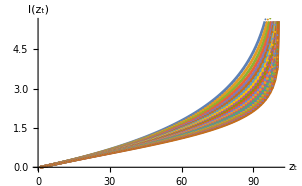

```mathematica
rlzt=Table[NIntegrate[(2 z)/(√(-z^2 +z0^2))1/(√f[z])/.f->Function[{z1},Interpolation[Transpose[{Table[i,{i,0,1,0.01}][[;;Length[out[[j]]]]],out[[j,All,1]]}]][z1]],{z,0,z0}],{j,Length[out]},{z0,0,1,0.01}];
Show[{ListPlot[lzt[[All,All,1]],AxesLabel->{Subscript[z, t],l[Subscript[z, t]]},Joined->True],ListPlot[rlzt,AxesLabel->{Subscript[z, t],l[Subscript[z, t]]}]}]
```

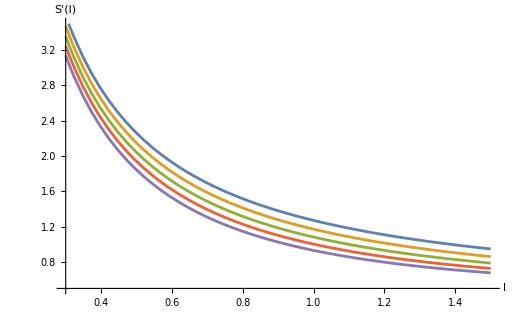

```mathematica
Show[Plot[S'[l]/. p->plist/.zh-> 1//Evaluate,{l,0.3,1.5},AxesLabel->{l,"S"'[l]},PlotRange->{0.5,3.5}],ListPlot[Table[Transpose[{rlzt[[i]],1/(2Table[z0,{z0,0,1,0.01}])}],{i,Length[rszt]}],PlotTheme->"Detailed",PlotStyle->Directive[PointSize[0.013]]]]
```

```mathematica
model=LinearModelFit[out,{x,y},{x,y}];
fittedFunction=model["Function"];
(*Example output:f[x,y]=0.5+4 x+0.6 y*)
```

LinearModelFit::notdata: The first argument is not a vector, matrix, or a list containing a design matrix and response vector.

```mathematica
zpf=Table[{Table[0.01 j ,{j,0,100}][[j]],Table[0.1i,{i,0,20}][[i]],out[[i,j,1]]},{i,21},{j,100}];
zpf=Flatten[zpf,1];
```

```mathematica
model=GeneralizedLinearModelFit[zpf,{x(*,y*),x^2,x y(*,y^2*),x^3(*,y^3*),x^2 y,x y^2,x^4(*,y^4*)(*,x y^3*),y x^3,x^2 y^2,x^5(*,y^5*),x^4 y(*,y^4 x*),x^3 y^2(*,x^2 y^3*)},{x,y}];
fittedFunction=model["Function"][z,p];
(#[[3]]-fittedFunction/.Thread[{z,p}-> #[[{1,2}]]])^2/Length[zpf]&/@zpf//Total
Collect[fittedFunction//FullSimplify,z]
```

9.42714×10^-7

1.00077+(-1.30084+1.31708 p-0.0246912 p^2) z+(0.508003-1.65927 p+0.32152 p^2) z^2+(-0.735097+0.486013 p-0.294639 p^2) z^3+(0.788506-0.137347 p) z^4-0.267425 z^5

```mathematica
Show[{ListPlot3D[zpf,PlotStyle->Gray],Plot3D[{fittedFunction},{z,0,1},{p,0,2},PlotPoints->30]}]
```

-Graphics3D-

#### (l/(2zh) +ⅇ^(l/(2 zh))(l/(2zh))^p)/(1+ (l/(2zh))^p)

S[l]=L/(2 G_3)Log[(2zh)/(ϵ_UV p) Tanh[l/(2zh)p]ⅇ^(l/(2zh))]

```mathematica
S[l_]:=Log[(2 zh)/Subscript[ϵ, UV] (l/(2zh) +ⅇ^(l/(2 zh))(l/(2zh))^p)/(1+ (l/(2zh))^p)];
(*plist=Table[0.1i+2,{i,0,23}]//N;*)
plist=Table[0.5i+1.8,{i,0,5}]
```

{1.8,2.3,2.8,3.3,3.8,4.3}

```mathematica
Series[S[l]/.p-> 0,{l,0,3}]
```

Log[zh/ϵ_UV]+l/zh-(3 l^2)/(8 zh^2)+(11 l^3)/(48 zh^3)+O[l]^4

```mathematica
Dynamic[Show[plotf[out](*,Plot[1-z,{z,0,1},PlotStyle-> Gray]*)]]
```

```mathematica
lzt=findlzt[plist]; 
out = predict[lzt];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.968691}. NIntegrate obtained 6.23314-1.97745 ⅈ and 0.0745403 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.961445}. NIntegrate obtained 5.21234-1.03324 ⅈ and 0.052686 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.961445}. NIntegrate obtained 4.96707-0.79513 ⅈ and 0.0408662 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

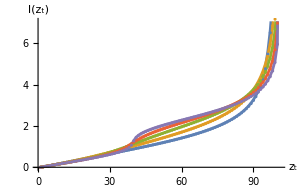

```mathematica
rlzt=Table[NIntegrate[(2 z)/(√(-z^2 +z0^2))1/(√f[z])/.f->Function[{z1},Interpolation[Transpose[{Table[i,{i,0,1,0.01}][[;;Length[out[[j]]]]],out[[j,All,1]]}]][z1]],{z,0,z0}],{j,Length[out]},{z0,0,1,0.01}];
Show[{ListPlot[lzt[[All,All,1]],AxesLabel->{Subscript[z, t],l[Subscript[z, t]]},Joined->True],ListPlot[rlzt,AxesLabel->{Subscript[z, t],l[Subscript[z, t]]}]}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

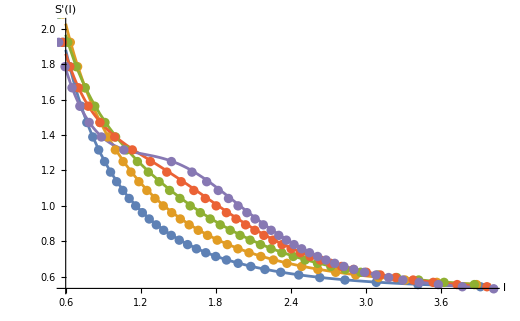

```mathematica
Show[Plot[S'[l]/. p->plist/.zh-> 1//Evaluate,{l,0.6,4},AxesLabel->{l,"S"'[l]}(*,PlotRange->{0.5,4}*)],ListPlot[Table[Transpose[{rlzt[[i]],1/(2Table[z0,{z0,0,1,0.01}])}][[;;;;2]],{i,Length[rlzt]}],PlotTheme->"Detailed",PlotStyle->Directive[PointSize[0.013]]]]
```

```mathematica
zpf=Table[{Table[0.01 j ,{j,0,100}][[j]],plist[[i]],out[[i,j,1]]},{i,Length[plist]},{j,100}];
zpf=Flatten[zpf,1];
```

```mathematica
MonomialsExact[vars_List,p_Integer?NonNegative]:=Module[{n=Length@vars},(Times@@(vars^#))&/@Select[Tuples[Range[0,p],n],Total[#]==p&]];
MonomialsExact[{x,y},4]
```

{y^4,x y^3,x^2 y^2,x^3 y,x^4}

```mathematica
model=GeneralizedLinearModelFit[zpf,Flatten[Table[MonomialsExact[{x,y},i],{i,30}]],{x,y}];
fittedFunction=model["Function"][z,p];
(#[[3]]-fittedFunction/.Thread[{z,p}-> #[[{1,2}]]])^2/Length[zpf]&/@zpf//Total
Collect[fittedFunction//FullSimplify,z]
```

0.0000456434

9718.04-28844.9 p+34947.2 p^2-21253.1 p^3+5905.45 p^4-23.924 p^5-309.735 p^6+2.46499 p^7+16.246 p^8+1.48424 p^9-0.637167 p^10-0.179045 p^11-0.000343019 p^12+0.0090412 p^13+0.00196836 p^14-0.0000104636 p^15-0.000101942 p^16-0.0000241762 p^17-8.52634×10^-7 p^18+9.99424×10^-7 p^19+2.92779×10^-7 p^20+2.26588×10^-8 p^21-9.07474×10^-9 p^22-3.27432×10^-9 p^23-2.82639×10^-10 p^24+1.04987×10^-10 p^25+3.30594×10^-11 p^26-7.83261×10^-13 p^27-1.74094×10^-12 p^28+1.97892×10^-13 p^29-3.99518×10^-15 p^30+(-12563.2+45625.2 p-63254.6 p^2+41094.2 p^3-10634.7 p^4-922.2 p^5+742.913 p^6+83.2995 p^7-38.4877 p^8-10.4439 p^9+0.508656 p^10+0.722429 p^11+0.129799 p^12-0.0111581 p^13-0.0102675 p^14-0.00203863 p^15+0.0000356161 p^16+0.000124689 p^17+0.0000325179 p^18+2.07753×10^-6 p^19-1.23656×10^-6 p^20-4.5447×10^-7 p^21-5.28624×10^-8 p^22+1.1752×10^-8 p^23+5.82788×10^-9 p^24+6.12479×10^-10 p^25-2.26989×10^-10 p^26-6.43973×10^-11 p^27+1.56266×10^-11 p^28-7.94276×10^-13 p^29) z+(-99375.1+235195. p-193740. p^2+51700.7 p^3+10330.5 p^4-5370.87 p^5-857.359 p^6+273.098 p^7+92.8164 p^8+0.773214 p^9-5.19941 p^10-1.27305 p^11-0.0360379 p^12+0.0601208 p^13+0.0190008 p^14+0.00232752 p^15-0.000324648 p^16-0.000227503 p^17-0.0000541802 p^18-4.75597×10^-6 p^19+1.52213×10^-6 p^20+7.6856×10^-7 p^21+1.57689×10^-7 p^22+2.91871×10^-9 p^23-9.12018×10^-9 p^24-2.76919×10^-9 p^25-1.54737×10^-11 p^26+2.22166×10^-10 p^27-2.26061×10^-11 p^28) z^2+(48054.8-406810. p+596280. p^2-319196. p^3+41728. p^4+15150.5 p^5-1594.21 p^6-989.13 p^7-84.3424 p^8+34.5499 p^9+12.886 p^10+1.56889 p^11-0.261794 p^12-0.167245 p^13-0.037453 p^14-0.00238697 p^15+0.00139016 p^16+0.000591713 p^17+0.000111819 p^18+1.68656×10^-6 p^19-5.95522×10^-6 p^20-1.92974×10^-6 p^21-2.20443×10^-7 p^22+5.35807×10^-8 p^23+2.67035×10^-8 p^24+1.91687×10^-9 p^25-1.68962×10^-9 p^26+1.33695×10^-10 p^27) z^3+(1.36035×10^6-2.04866×10^6 p+964421. p^2-45907.5 p^3-55635.8 p^4-5253.21 p^5+3341.78 p^6+1047.56 p^7+0.47992 p^8-67.7411 p^9-17.3049 p^10-0.638665 p^11+0.811549 p^12+0.271472 p^13+0.0376919 p^14-0.0024753 p^15-0.00259571 p^16-0.000673629 p^17-0.0000885148 p^18+1.97585×10^-6 p^19+4.29746×10^-6 p^20+1.29619×10^-6 p^21+2.53167×10^-7 p^22+2.3097×10^-8 p^23-1.04528×10^-8 p^24-5.98208×10^-9 p^25+8.44402×10^-10 p^26) z^4+(-2.85352×10^6+4.53171×10^6 p-2.5747×10^6 p^2+480378. p^3+81417. p^4-21279.5 p^5-4777.57 p^6+371.892 p^7+246.164 p^8+30.1154 p^9-2.30702 p^10-1.59721 p^11-0.473011 p^12-0.143273 p^13-0.0362227 p^14-0.00386851 p^15+0.00162394 p^16+0.00101706 p^17+0.000281638 p^18+0.0000344166 p^19-6.26442×10^-6 p^20-4.15822×10^-6 p^21-8.49588×10^-7 p^22+3.12911×10^-8 p^23+5.68205×10^-8 p^24-4.18377×10^-9 p^25) z^5+(1.23625×10^6-1.20899×10^6 p-204439. p^2+95428.9 p^3-29934. p^4-14983.4 p^5-790.172 p^6+436.879 p^7+87.9456 p^8+13.6921 p^9+9.26972 p^10+4.52601 p^11+1.21904 p^12+0.151071 p^13-0.0224409 p^14-0.0173498 p^15-0.00521002 p^16-0.00107294 p^17-0.000163834 p^18-0.0000146854 p^19+2.79221×10^-6 p^20+2.3952×10^-6 p^21+8.69324×10^-7 p^22+1.33325×10^-7 p^23-4.98221×10^-8 p^24) z^6+(1.95718×10^6+196288. p+2.65317×10^6 p^2-129148. p^3+37590.1 p^4+35042.9 p^5+5684.32 p^6-911.215 p^7-732.656 p^8-220.443 p^9-42.5703 p^10-4.76089 p^11+0.248299 p^12+0.313534 p^13+0.109938 p^14+0.0292632 p^15+0.00681925 p^16+0.00146661 p^17+0.000291291 p^18+0.0000451232 p^19-9.86297×10^-7 p^20-4.83223×10^-6 p^21-1.86512×10^-6 p^22+2.95572×10^-7 p^23) z^7+(-1.09554×10^7-9.9407×10^6 p-2.31474×10^6 p^2-1.44404×10^6 p^3-183035. p^4-928.883 p^5+5400.67 p^6+2938.39 p^7+1103.62 p^8+275.963 p^9+41.2684 p^10+0.469884 p^11-1.86966 p^12-0.725956 p^13-0.203696 p^14-0.0526323 p^15-0.0128576 p^16-0.00265724 p^17-0.000365133 p^18-8.51343×10^-6 p^19+4.05724×10^-6 p^20-1.97167×10^-6 p^21+1.03518×10^-6 p^22) z^8+(4.06731×10^7+2.22717×10^7 p+7.62534×10^6 p^2+1.6875×10^6 p^3+308713. p^4-10558.7 p^5-18966.2 p^6-4056.74 p^7-250.102 p^8+61.0134 p^9+19.154 p^10+5.06643 p^11+2.35159 p^12+1.01161 p^13+0.315023 p^14+0.0719116 p^15+0.0130601 p^16+0.00254209 p^17+0.000727948 p^18+0.00020254 p^19+0.0000231892 p^20-7.05561×10^-6 p^21) z^9+(-7.70132×10^7-3.07703×10^7 p-8.97805×10^6 p^2-1.09718×10^6 p^3-53261.5 p^4-37847.2 p^5-17175.7 p^6-4027.65 p^7-847.525 p^8-256.634 p^9-83.5241 p^10-20.8135 p^11-3.64297 p^12-0.501572 p^13-0.121632 p^14-0.0558537 p^15-0.0205773 p^16-0.00508824 p^17-0.000824678 p^18-0.000115995 p^19-0.0000302797 p^20) z^10+(5.81433×10^7+1.20392×10^7 p-1.04238×10^6 p^2+159093. p^3+273792. p^4+114785. p^5+35356.2 p^6+9038.39 p^7+1872.15 p^8+302.328 p^9+40.2367 p^10+6.81101 p^11+1.9814 p^12+0.551699 p^13+0.10484 p^14+0.013349 p^15+0.002943 p^16+0.00158544 p^17+0.000661563 p^18+0.00032041 p^19) z^11+(4.34312×10^7+2.88464×10^7 p+5.40624×10^6 p^2+83979.3 p^3-183984. p^4-26083.6 p^5-69.4576 p^6+147.928 p^7+8.21445 p^8+28.6202 p^9+15.1927 p^10+3.9333 p^11+0.763599 p^12+0.260775 p^13+0.135792 p^14+0.0510152 p^15+0.0092998 p^16-0.00111309 p^17-0.00022994 p^18) z^12+(-8.90793×10^7-1.39902×10^7 p+785418. p^2-780552. p^3-539779. p^4-136914. p^5-34344.5 p^6-9126.99 p^7-1819.62 p^8-228.942 p^9-26.4358 p^10-10.4752 p^11-4.1272 p^12-0.802546 p^13-0.0192518 p^14+0.00194401 p^15-0.0194604 p^16-0.00535912 p^17) z^13+(-4.67761×10^7-3.06109×10^7 p-562272. p^2+625925. p^3+86780.7 p^4+45628.1 p^5+5242.25 p^6-1246.59 p^7+5.6649 p^8+194.314 p^9+44.7726 p^10-3.78342 p^11-3.30964 p^12-0.276712 p^13+0.118755 p^14-0.00222052 p^15+0.0112834 p^16) z^14+(9.67103×10^7-2.76031×10^6 p+1.11425×10^6 p^2+1.71475×10^6 p^3+552110. p^4+188745. p^5+37537.8 p^6+5025.22 p^7+1215.53 p^8+396.839 p^9+68.9319 p^10+1.72463 p^11-0.159637 p^12+0.636925 p^13+0.154613 p^14+0.104241 p^15) z^15+(9.52615×10^7+2.1222×10^7 p-1.7694×10^6 p^2+7203.14 p^3-13059.2 p^4+52521.5 p^5+6742.57 p^6-2111.3 p^7-446.382 p^8+26.6167 p^9+5.82413 p^10-1.80953 p^11+0.0474943 p^12-0.46751 p^13-0.161693 p^14) z^16+(-5.58625×10^7+1.76131×10^7 p-5.85547×10^6 p^2-1.95029×10^6 p^3-757463. p^4-126419. p^5-27455.5 p^6-8461.01 p^7-1678.98 p^8-179.19 p^9-6.78388 p^10-0.133225 p^11-3.2514 p^12-1.8961 p^13) z^17+(-1.44808×10^8+3.62904×10^6 p-2.99015×10^6 p^2-766909. p^3-589302. p^4-66664.9 p^5-4323.23 p^6-2365.45 p^7-433.616 p^8+62.1798 p^9+38.6813 p^10+4.54485 p^11+1.93035 p^12) z^18+(-4.96965×10^7-4.82951×10^6 p+5.14299×10^6 p^2+2.44122×10^6 p^3+183369. p^4+127232. p^5+39172.6 p^6+5392.56 p^7+605.976 p^8+115.771 p^9+23.4454 p^10+36.35 p^11) z^19+(1.15263×10^8-1.19324×10^7 p+7.96006×10^6 p^2+3.36435×10^6 p^3+366000. p^4+144396. p^5+30061. p^6+1180.74 p^7-472.353 p^8-222.036 p^9-8.86394 p^10) z^20+(1.50703×10^8-2.04673×10^7 p+287666. p^2+345579. p^3-346078. p^4-53301.8 p^5-20435.8 p^6-4806.42 p^7-405.442 p^8-641.066 p^9) z^21+(8.4592×10^6-1.50335×10^7 p-9.53856×10^6 p^2-2.87324×10^6 p^3-775471. p^4-148770. p^5-24170.6 p^6+6952.17 p^7+159.197 p^8) z^22+(-1.49982×10^8+1.70246×10^7 p-8.92552×10^6 p^2-1.45886×10^6 p^3+101222. p^4+10847.7 p^5+23713.9 p^6+11138.5 p^7) z^23+(-1.31205×10^8+5.00065×10^7 p+2.2273×10^6 p^2+3.24075×10^6 p^3+1.05862×10^6 p^4-9536.24 p^5-22071.7 p^6) z^24+(5.62901×10^7+2.78334×10^7 p+8.65238×10^6 p^2+2.66236×10^6 p^3-188766. p^4-203129. p^5) z^25+(1.70626×10^8-5.60535×10^7 p+971271. p^2-6.69886×10^6 p^3+996302. p^4) z^26+(1.68356×10^7-7.62817×10^7 p-1.88644×10^6 p^2-17248.2 p^3) z^27+(-1.78494×10^8+1.03552×10^8 p+3.05652×10^6 p^2) z^28+(9.01808×10^7-3.30025×10^7 p) z^29-1.0274×10^7 z^30

```mathematica
Show[{ListPlot3D[zpf,PlotStyle->Gray],Plot3D[{fittedFunction},{z,0,1},{p,plist[[1]],plist[[-1]]},PlotPoints->30]}]
```

-Graphics3D-

#### Sin

S[l]=L/(2 G_3)Log[2/ϵ_UV Sin[l/2]];

```mathematica
S[l_]:=Log[(2 p)/Subscript[ϵ, UV] Sin[l/(2 p)]];
plist={1,2,3,4};
```

```mathematica
Limit[S[l]/l,l-> ∞]
```

lim_(l→∞) Log[(2 p Sin[l/(2 p)])/ϵ_UV]/l

dS/dl=1/(2 z_t)

```mathematica
Dynamic[Show[plotf[out],Plot[{1+z^2,1+(z/2)^2,1+(z/3)^2,1+(z/4)^2},{z,0,2},PlotLegends->plist]]]
```

```mathematica
lzt=findlzt[plist];
out = predict[lzt];
```

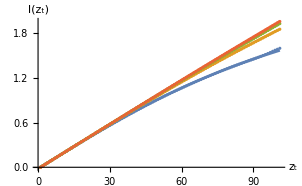

```mathematica
rlzt=Table[NIntegrate[(2 z)/(√(-z^2 +z0^2))1/(√f[z])/.f->Function[{z1},Interpolation[Transpose[{Table[i,{i,0,1,0.01}][[;;Length[out[[j]]]]],out[[j,All,1]]}]][z1]],{z,0,z0}],{j,Length[out]},{z0,0,1,0.01}];
Show[{ListPlot[lzt[[All,All,1]],AxesLabel->{Subscript[z, t],l[Subscript[z, t]]},Joined->True],ListPlot[rlzt,AxesLabel->{Subscript[z, t],l[Subscript[z, t]]}]}]
```

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

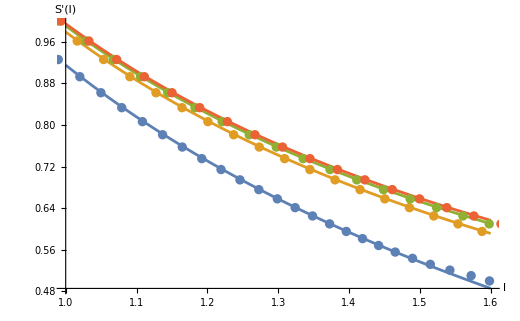

```mathematica
Show[Plot[S'[l]/. p->plist/.zh-> 1//Evaluate,{l,1,1.6},AxesLabel->{l,"S"'[l]}(*,PlotRange->{0.5,4}*)],ListPlot[Table[Transpose[{rlzt[[i]],1/(2Table[z0,{z0,0,1,0.01}])}][[;;;;2]],{i,Length[rlzt]}],PlotTheme->"Detailed",PlotStyle->Directive[PointSize[0.013]]]]
```